# Praktikaren deskribapena

Praktika honetan, zenbaki konplexuen arteko zenbait eragiketa egingo ditugu, hala nola, erroketa, logaritmo nepertarra, esponentziala eta berreketa. Ondoren, ekuazioak ebatziko ditugu ℂ plano konplexuan. Bukatzeko, ekuazio berezi bat ebatziko dugu.

Praktikan zehar Mathematica-ko agindu batzuk aurkituko dituzu (hizki larriz hasten dira). Agindu horiek adibideak dira; alde batetik, agindua bera nola erabili behar den ikusteko balioko dute; beste aldetik, ariketen orriko ariketak ebazten laguntzeko balioko dute.   Agindu horiek exekutatu behar dituzu.

Praktikan zehar Mathematica-ko aginduen bidez definitutako funtzio batzuk ikusiko dituzu (hizki xehez hasten dira). Funtzio horiekin ebatziko ditugu ariketak, urrats batean edo zenbait urratsetan. Funtzio horiek exekutatu behar dituzu; ondoren, ariketen orriko ariketa egokiekin proba batzuk egin behar dituzu, ariketak aipatuz.

# Zenbaki konplexuen eragiketak

Atal honetan, zenbaki konplexuen arteko zenbait eragiketa egingo ditugu, hala nola, erroketa, logaritmo nepertarra, esponentziala eta berreketa.

## Zenbaki konplexuak: modulua eta argumentua

Zenbaki konplexuak 𝓏==𝒶+𝒷𝒾 motako zenbakiak dira, non 𝒾^2==-1 baita; 𝓏==𝒶+𝒷𝒾 zenbaki konplexua OXY planoko (𝒶,𝒷) puntuarekin bat dator. 𝓏-ren 𝒶 koordenatua zati erreala da, eta 𝓏-ren 𝒷 koordenatua zati irudikaria. 𝓏==𝒶+𝒷𝒾 adierazpenari binomial deritzo, eta (𝒶,𝒷) adierazpenari geometriko. Mathematica-k balio horiek ematen dituzten funtzioak definiturik dauzka: Re eta Im, zati erreala eta zati irudikaria. Kontuan izan guk “𝒾” idazten duguna Mathematica-k “I” idazten duela.

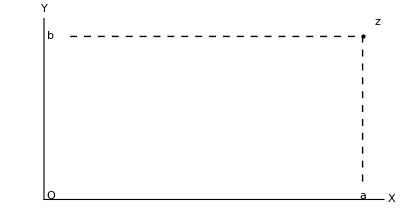

```mathematica
p=Graphics[{Text["z",{2.1,1.1}],Point[{2,1}]}];
lk=Graphics[{Dashed,Text["O",{-0.1,-0.1}],Text["a",{2,-0.1}],Text["b",{-0.1,1}],Line[{{2,0},{2,1},{0,1}}]},Axes->True,Ticks->None,AxesLabel->{X,Y}];
Show[lk,p]
```

Zenbaki konplexuak, planoko puntuak bezala, beren jatorrirako ρ distantziaren eta dagokion zuzenkiak OX ardatzarekin osatzen duen θ angeluaren bidez defini daitezke; jatorrirako distantzia 𝓏-ren modulua da, eta angelua 𝓏-ren argumentua. Kasu horretan, 𝓏==ρ_θ adierazpenari polar deritzo. Mathematica-k balio horiek ematen dituzten funtzioak definiturik dauzka: Abs eta Arg, modulua eta argumentua.

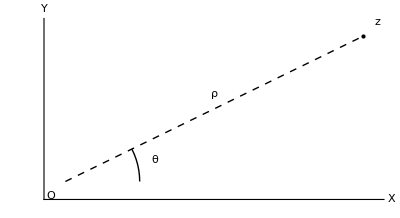

```mathematica
lp=Graphics[{Dashed,Text["O",{-0.1,-0.1}],Text["ρ",{1,0.6}],Text["θ",{0.6,0.15}],Line[{{0,0},{2,1}}]},Axes->True,Ticks->None,AxesLabel->{X,Y}];
arku=Graphics[Circle[{0,0},0.5,{0,ArcTan[1/2]}]];
Show[lp,arku,p]
```

1) Ebatz itzazu ariketen orriko ariketa batzuk aurreko lau aginduekin (esan zer ariketa diren).

11 - 4 ariketa

```mathematica
Re[3/I]
```

0

```mathematica
Im[3/I]
```

-3

```mathematica
Arg[3/I]
```

-π/2

```mathematica
Abs[3/I]
```

3

10 - 2ariketa

```mathematica
Re[((2+I)/(1-I))+((2-I)/(1+I))]
```

1

```mathematica
Im[((2+I)/(1-I))+((2-I)/(1+I))]
```

0

```mathematica
Arg[((2+I)/(1-I))+((2-I)/(1+I))]
```

0

```mathematica
Abs[((2+I)/(1-I))+((2-I)/(1+I))]
```

1

## Zenbaki konplexuen erroen kalkulua

Orain, zenbaki konplexuen erroketa egingo dugu; bukaeran, emaitzen irudia egingo dugu. Zenbaki konplexuen adierazpen polarra erabiliko dugu; horretarako 𝓏 zenbaki konplexuaren ρ modulua eta θ argumentua ezagutu behar ditugu:  𝓏==ρ_θ. Erroketen formula hau da:
						 𝓏^(1/𝓃)==ρ_θ^(1/𝓃)==(ρ^(1/𝓃))_((θ+2𝓀π)/𝓃),  𝓀∈ℤ. 
				
Beraz, zenbaki konplexu baten 𝓃-erroak kalkulatu nahi baditugu, emaitzen moduluak eta argumentuak kalkulatu beharko ditugu. Lehenik, emaitzen modulua kalkulatzeko, moduluaren 𝓃-erroa zenbaki erreal moduan kalkulatuko dugu, eta, ondoren, argumentua gehi 2kπ birak batu eta zati 𝓃 egingo dugu.

Emaitza guztiek modulu bera dute,  ρ^(1/𝓃).

2) Zer irudi geometriko osatzen dute modulu bera duten zenbaki konplexuek? (Galdera orokorra)

Zirkunferentzia bat osatzen dute, jatorritik, (0,0) puntutik distantzia berdinera daudelako. Erradioa?

3) Zenbat erro ematen ditu erroketak?

Infinitu erro ematen ditu k edozein zenbaki oso izan daitekeelako. Beraz, infinitu argumentu desberdin lortuko ditugu baina infinitu horietatik n bakarrik dira desberdinak.

4) Esan zehazki non dauden zenbaki konplexu baten erro guztiak?

Jatorritik ρ^(1/𝓃) distantziara daude erro guztiak, ρ^(1/𝓃)-ko erradio bat duen zirkunferentzia batean.

𝓏 zenbaki konplexuaren erroen modulua kalkulatuko duen funtzioa definituko dugu.

```mathematica
erromod[x_,n_] := (Abs[x])^(1/n)
erromod[I-2,1]
```

√5

```mathematica
N[16^(1/5)]
```

1.7411

5) Zenbat dira desbedin?

Infinitu erro egon arren, n errok bakarrik izango dute argumentu desberdina.

Egin dezagun proba zenbaki baten 4-erroarekin. Hurrengo aginduan k-ren balioak aldatuko ditugu ikusteko zenbat argumentu lor ditzakegun:

```mathematica
Table[ Arg[ (8Sqrt[2]-8Sqrt[2]I)^(1/4) ]+2k Pi/4,{k,-3,7} ]
```

{-(25 π)/16,-(17 π)/16,-(9 π)/16,-π/16,(7 π)/16,(15 π)/16,(23 π)/16,(31 π)/16,(39 π)/16,(47 π)/16,(55 π)/16}

k-ren balioak aldatzekotan, hobe da aldagai moduan definitzea, funtzio honetan bezala:

```mathematica
argumentuak[x_,n_,k_]:= Table[ (Arg[x]+2l Pi)/n,{l,-k,k} ]
```

Orain, argumentu desberdinak bakarrik emango dituen funtzioa definituko dugu.

```mathematica
erroarg[x_,n_]:= Table[ (Arg[x]+2k Pi)/n, {k,0,n-1} ]
erroarg[I-2,1]
```

{π-ArcTan[1/2]}

## Zenbaki konplexuen erroen irudia

Irudia egiteko OXY planoko puntuak osatuko ditugu erroen moduluarekin eta argumentuekin; horretarako, koordenatu kartesiarretarako aldagai-aldaketaren formulak erabiliko ditugu.

```mathematica
erroak[x_,n_] := Map[ Point,
                      Table[ {erromod[x,n] Cos[erroarg[x,n][[i]]], erromod[x,n] Sin[erroarg[x,n][[i]]]},
			                 {i,n} ] ]
erroak[I/1+1,2]
```

{Point[{2^(1/4) Cos[π/8],2^(1/4) Sin[π/8]}],Point[{-2^(1/4) Cos[π/8],-2^(1/4) Sin[π/8]}]}

Orain, erroak eta dagokien zirkunferentzia irudikatuko ditugu OXY planoan.

```mathematica
erroiru[x_,n_]:=Show[Graphics[{{RGBColor[1,0,0],PointSize[0.015],erroak[x,n]},
                                                                 Circle[{0,0},erromod[x,n]]}],
                                             AspectRatio->Automatic,Axes->True]
```

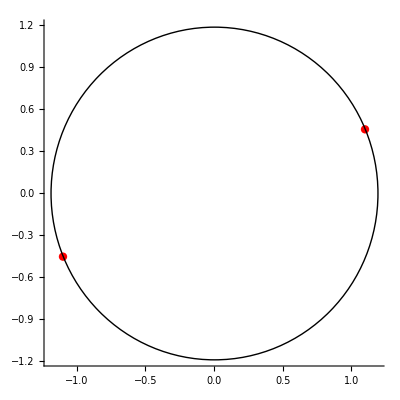

```mathematica
erroiru[1+I,2]
```

## Zenbaki konplexuen logaritmo nepertarra

Atal honetan zenbaki konplexuen logaritmo nepertarra kalkulatuko dugu. Ondoren logaritmoaren emaitzaren irudia egingo dugu. Horrez gain, logaritmoaren balio nagusia ere kalkulatuko dugu.
Logaritmo nepertarra kalkulatzeko adierazpide polarra erabiliko dugu, hau da, 𝓏==ρ_θ idazkera erabiliko dugu. Logaritmo nepertarraren formula hau da:
					ln 𝓏 ==ln ρ_θ==ln ρ + (θ+2𝓀π)𝒾, 𝓀∈ℤ  izanik.

6) Zein da emaitzaren adierazpidea?

Zenbaki konplexuen logaritmo nepretarraren adierazpidea binomiala da eta ln ρ  zati erreala den eta (θ+2𝓀π) zati irudikaria dira

7) Zenbat logaritmo nepertar ematen ditu formulak?

Infinitu logaritmo nepertar ematen ditu formulak eta k zenbaki osoa delako

8) Zer dute komunean emaitzek eta zer desberdin?

Emaitza guztiek zati erreal berbera dute, zati irudikarian desberditzen diran, non ondoz ondoko emaitzen artean 2π-ko aldea dagoen.

Zati erreala ez da 𝓀-ren arabera aldatzen.

9) Zer esanahi geometriko du horrek? (Galdera orokorra)

Logaritmo nepertarraren emaitza guztiak zuzen bertikal batean daudela.

10) Non daude zehazki zenbaki konplexu baten logaritmo nepertar guztiak?

Zuzen batean, x=ln ρ  zuzenean hain zuzen ere.

Funtzio honekin zenbaki konplexu baten hainbat logaritmo baino ez dugu lortuko:

```mathematica
ln[z_,k_] := Table[ Log[Abs[z]]+(Arg[z]+2l Pi) I, {l,-k,k} ]
ln[I+1,2]
```

{-(15 ⅈ π)/4+Log[2]/2,-(7 ⅈ π)/4+Log[2]/2,(ⅈ π)/4+Log[2]/2,(9 ⅈ π)/4+Log[2]/2,(17 ⅈ π)/4+Log[2]/2}

Orain, funtzio honekin zenbaki konplexuaren nahi adina logaritmo irudikatuko dugu:

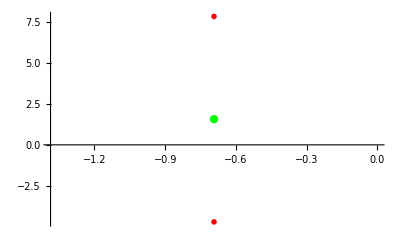

```mathematica
lniru[z_,k_] := If[k==0,ListPlot[{{Re[ln[z,k][[k+1]]],Im[ln[z,k][[k+1]]]}},
                                                      PlotStyle->{RGBColor[0,1,0], PointSize[0.015]} ],ListPlot[ {Table[{Re[ln[z,k][[i]]],Im[ln[z,k][[i]]]},{i,k} ],
                                                         {{Re[ln[z,k][[k+1]]],Im[ln[z,k][[k+1]]]}},
                                                          Table[{Re[ln[z,k][[i]]],Im[ln[z,k][[i]]]},{i,k+2,2k+1} ]},
                                                           PlotStyle->{{RGBColor[1,0,0],PointSize[0.01]},
                                                                                     {RGBColor[0,1,0], PointSize[0.015]},
                                                                                     {RGBColor[1,0,0],PointSize[0.01]}} ]]
lniru[I/2,1]
```

11) Aurreko funtzioa erabiliz, puntu berde bat agertzen da, zer kasutan lortzen da?

Puntu berdea 𝓀=0 kasuan lortzen da. Kasu honetan logaritmoaren balio nagusia lortzen da.

12) Ariketen orriko ariketa batzuk aurreko funtzioarekin ebatz daitezke; aukera ezazu bat, eta ebatz ezazu.

```mathematica
25  5Ariketa
```

{ⅈ (-π/2-2 √3 π),ⅈ (-π/2+2 (1-√3) π),ⅈ (-π/2+2 (2-√3) π),ⅈ (-π/2+2 (3-√3) π)}

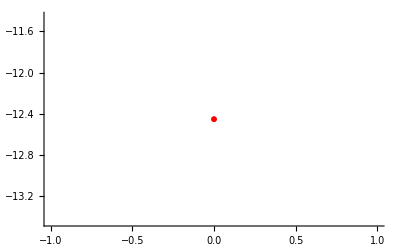

```mathematica
ln[-I,3^(1/2)]
lniru[-I,3^(1/2)]
```

```mathematica
25  4Ariketa
```

{-(5 ⅈ π)/2,-(ⅈ π)/2,(3 ⅈ π)/2}

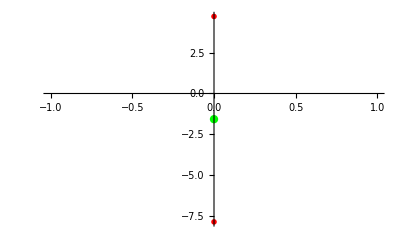

```mathematica
ln[-I,1]
lniru[-I,1]
```

Horiek kalkuluak baino ez dira; ekuazioak ebatzi behar ziren.

Zenbaki konplexu baten logaritmo guztietatik logaritmoaren balio nagusi deritzo 𝓀 == 0 eginez lortzen den logaritmoari . Funtzio honekin zenbaki konplexu baten logaritmo nepertarraren balio nagusia kalkulatuko dugu:

```mathematica
lnna[z_]:= Log[Abs[z]] + Arg[z] I
lnna[-I+3]
```

-ⅈ ArcTan[1/3]+Log[10]/2

Funtzio honekin zenbaki konplexu baten logaritmo nepertarraren balio nagusia irudikatuko dugu:

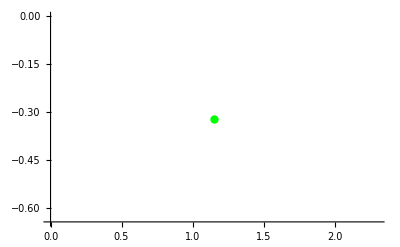

```mathematica
lnnairu[z_] := ListPlot[ {{Re[lnna[z]],Im[lnna[z]]}},
					     PlotStyle->{RGBColor[0,1,0],
								     PointSize[0.015]}]
lnnairu[-I+3]
```

## Zenbaki konplexuen esponentziala

Atal honetan zenbaki konplexuen esponentziala kalkulatuko dugu. Logaritmoak ez bezala esponentzialak emaitza bakarra emango du. Esponentziala kalkulatzeko zenbaki konplexuaren adierazpen binomiala erabiliko dugu. Esponentzialaren formula hau da:
					e^𝓏==e^(𝒶+𝒷𝒾)==e^𝒶 e^𝒷𝒾==e^𝒶(Cos 𝒷 + 𝒾 Sin 𝒷)

13) Zein da emaitzaren adierazpidea?

Emaitzaren adierazpidea trigonometrikoa da, Euler-en formula erabiliz lortzen dena.

14) Zenbat esponentzial ematen ditu formulak? Eman ezazu azalpena.

Bakarra da,e^a. Cos b eta Sin b bakarrak direlako.

15) Zein da emaitzaren modulua eta argumentua? Eman ezazu azalpena.

Modulua e^𝒶 eta argumentua 𝒷. Adierazpide trigonometrikoan dagoenez  ρ_(Cosθ + 𝒾sinθ) forma izango baitu.

Formula hori funtzio honen bidez defini dezakegu:

```mathematica
esp[z_] := E^Re[z] (Cos[Im[z]] + I Sin[Im[z]])
esp[I+2]
```

ⅇ^2 (Cos[1]+ⅈ Sin[1])

16) Ariketen orriko ariketa bat aurreko funtzioarekin ebatz daiteke, ebatz ezazu.

24 Ariketa

```mathematica
esp[I^(1/2)]
```

ⅇ^(1/(√2)) (Cos[1/(√2)]+ⅈ Sin[1/(√2)])

```mathematica
esp[(1+I)^I]
```

ⅇ^Re[(1+ⅈ)^ⅈ] (Cos[Im[(1+ⅈ)^ⅈ]]+ⅈ Sin[Im[(1+ⅈ)^ⅈ]])

```mathematica
esp[2^(2I)]
```

ⅇ^Cos[2 Log[2]] (Cos[Sin[2 Log[2]]]+ⅈ Sin[Sin[2 Log[2]]])

```mathematica
esp[(2-I)^(1+I)]
```

ⅇ^Re[(2-ⅈ)^(1+ⅈ)] (Cos[Im[(2-ⅈ)^(1+ⅈ)]]+ⅈ Sin[Im[(2-ⅈ)^(1+ⅈ)]])

```mathematica
esp[(3+4I)^(1/3)]
```

ⅇ^Re[(3+4 ⅈ)^(1/3)] (Cos[Im[(3+4 ⅈ)^(1/3)]]+ⅈ Sin[Im[(3+4 ⅈ)^(1/3)]])

Horiek kalkuluak baino ez dira; ekuazioak ebatzi behar ziren.

## Zenbaki konplexuen berreketa

Atal honetan bi zenbaki konplexuren arteko berreketa kalkulatuko dugu. Berreketa kalkulatzeko logaritmo nepertarra erabiliko dugu formula honen bidez:
						𝓏^𝓌==e^(𝓌 ln 𝓏)

17) Zenbat berreketa ematen ditu formulak? Eman ezazu azalpena.

Infinitu, emaitzan logaritmo nepertarra dagoelako, eta honek infinitu emaitza ematen ditu. Beraz emaitza infinitu izango ditu k-ren balioaren araberakoak.

Horren arabera, berreketa kalkulatzeko logaritmo nepertarraren funtzioa erabiliko dugu. Funtzio honekin bi zenbaki konplexuren arteko berreketaren balioak kalkulatuko ditugu:

Funtzio honekin bi zenbaki konplexuren arteko berreketaren balio nagusia kalkulatuko dugu:

```mathematica
berreketa[z_,w_,k_]:=Exp[w*ln[z,k]]
berreketa[I-2,I/2,1]
```

{ⅇ^(1/2 ⅈ (ⅈ (-π-ArcTan[1/2])+Log[5]/2)),ⅇ^(1/2 ⅈ (ⅈ (π-ArcTan[1/2])+Log[5]/2)),ⅇ^(1/2 ⅈ (ⅈ (3 π-ArcTan[1/2])+Log[5]/2))}

Orain, berreturen irudia egingo dugu. Funtzio honekin bi zenbaki konplexuren arteko berreturen irudia egingo dugu:

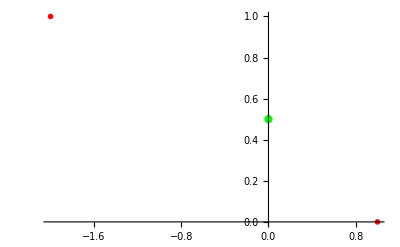

```mathematica
berreketairu[z_,w_,k_] := 
If[k==0,ListPlot[{{Re[berreketa[z,w,k][[k+1]]],Im[berreketa[z,w,k][[k+1]]]}}, PlotStyle->{RGBColor[0,1,0], PointSize[0.015]}],
 ListPlot[ {Table[{Re[berreketa[z,w,k][[i]]],Im[berreketa[z,w,k][[i]]]},{i,k} ],
                                            {{Re[berreketa[z,w,k][[k+1]]],Im[berreketa[z,w,k][[k+1]]]}},
                                            Table[{Re[berreketa[z,w,k][[i]]],Im[berreketa[z,w,k][[i]]]},{i,k+2,2k+1} ]},
                                              PlotStyle->{{RGBColor[1,0,0],PointSize[0.01]},
                                                                                     {RGBColor[0,1,0], PointSize[0.015]},
                                                                                     {RGBColor[1,0,0],PointSize[0.01]}} ]]
berreketairu[I-2,I/2,1]
```

18) Nola lortuko duzu berretura nagusia? Egin itzazu proba batzuk.

Esponentzialaren logaritmo nepertarrean k-ri 0 balioa emanez.

```mathematica
berreketa[I-2,I/1,0]
```

{ⅇ^(ⅈ (ⅈ (π-ArcTan[1/2])+Log[5]/2))}

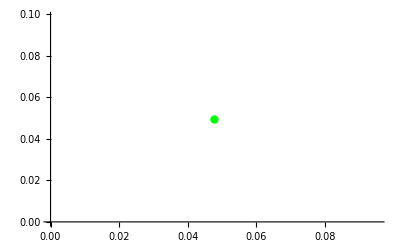

```mathematica
berreketairu[I-2,I/1,0]
```

```mathematica
berreketa[I/2-3,3+I/1,0]
```

{ⅇ^((3+ⅈ) (ⅈ (π-ArcTan[1/6])+Log[(√37)/2]))}

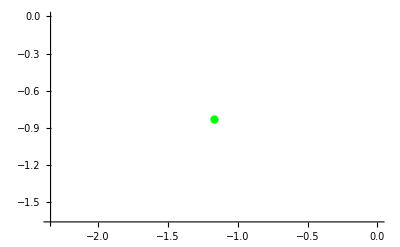

```mathematica
berreketairu[I/2-3,3+I/1,0]
```

```mathematica
berreketa[3I/5-4,4+I/1,0]
```

{ⅇ^((4+ⅈ) (ⅈ (π-ArcTan[3/20])+Log[(√409)/5]))}

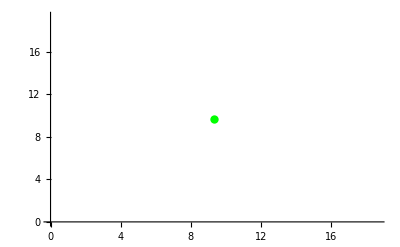

```mathematica
berreketairu[3I/5-4,4+I/1,0]
```

# Ekuazioen ebazpena

Atal honetan, ekuazioak ebatziko ditugu; ekuazioak zenbaki konplexuen ℂ multzoan ebatziko ditugu; hau da, ekuazioan erabiliko ditugun koefizienteak zenbaki konplexuak izango dira eta bilatuko ditugun soluzioak ere zenbaki konplexuak izango dira. Ekuazioaren soluzioak bilatu ondoren, soluzioak OXY planoan irudikatuko ditugu.
Kontuan izan behar dugu ekuazioak idazteko, berdintza == idatzi beharko dugula.
Mathematica-k ekuazioak ebazteko hainbat agindu ditu, hala nola, FindRoot, LinearSolve, NRoots, NSolve, Reduce, Roots, Solve. Agindu bakoitzak bere berezitasuna du. Guk, hemen, Solve erabiliko dugu; agindu horrek polinomioen erroak bilatzen ditu.

## Ekuazioaren soluzioak bilatzen

Ekuazio batzuen ebazpena egingo dugu Solve aginduaren bidez.

```mathematica
Solve[ 2z^4-z+2 == 0, z]
```

{{z→-1/2 √((9+ⅈ √12207)^(1/3)/(2 3^(2/3))+8/(3 (9+ⅈ √12207))^(1/3))-1/2 √(-(9+ⅈ √12207)^(1/3)/(2 3^(2/3))-8/(3 (9+ⅈ √12207))^(1/3)-1/(√((9+ⅈ √12207)^(1/3)/(2 3^(2/3))+8/(3 (9+ⅈ √12207))^(1/3))))},{z→-1/2 √((9+ⅈ √12207)^(1/3)/(2 3^(2/3))+8/(3 (9+ⅈ √12207))^(1/3))+1/2 √(-(9+ⅈ √12207)^(1/3)/(2 3^(2/3))-8/(3 (9+ⅈ √12207))^(1/3)-1/(√((9+ⅈ √12207)^(1/3)/(2 3^(2/3))+8/(3 (9+ⅈ √12207))^(1/3))))},{z→1/2 √((9+ⅈ √12207)^(1/3)/(2 3^(2/3))+8/(3 (9+ⅈ √12207))^(1/3))-1/2 √(-(9+ⅈ √12207)^(1/3)/(2 3^(2/3))-8/(3 (9+ⅈ √12207))^(1/3)+1/(√((9+ⅈ √12207)^(1/3)/(2 3^(2/3))+8/(3 (9+ⅈ √12207))^(1/3))))},{z→1/2 √((9+ⅈ √12207)^(1/3)/(2 3^(2/3))+8/(3 (9+ⅈ √12207))^(1/3))+1/2 √(-(9+ⅈ √12207)^(1/3)/(2 3^(2/3))-8/(3 (9+ⅈ √12207))^(1/3)+1/(√((9+ⅈ √12207)^(1/3)/(2 3^(2/3))+8/(3 (9+ⅈ √12207))^(1/3))))}}

```mathematica
Solve[ I z^2 + z^3 + 4 I z == 0, z]
```

{{z→0},{z→1/2 (-ⅈ-√(-1-16 ⅈ))},{z→1/2 (-ⅈ+√(-1-16 ⅈ))}}

19) Egin itzazu ariketen orriko ariketa batzuk aurreko funtzioa erabiliz. Esan ezazu zer ariketa diren.

20  6 Ariketa

```mathematica
Solve[2z^3-3z^2+5Iz==0,z]
```

{{z→1/2 (1+1/((1-10 Iz+2 √5 √(-Iz+5 Iz^2))^(1/3))+(1-10 Iz+2 √5 √(-Iz+5 Iz^2))^(1/3))},{z→1/2-(1+ⅈ √3)/(4 (1-10 Iz+2 √5 √(-Iz+5 Iz^2))^(1/3))-1/4 (1-ⅈ √3) (1-10 Iz+2 √5 √(-Iz+5 Iz^2))^(1/3)},{z→1/2-(1-ⅈ √3)/(4 (1-10 Iz+2 √5 √(-Iz+5 Iz^2))^(1/3))-1/4 (1+ⅈ √3) (1-10 Iz+2 √5 √(-Iz+5 Iz^2))^(1/3)}}

20  15 Ariketa

```mathematica
Solve[z^4+1-I==0,z]
```

{{z→-(-1+ⅈ)^(1/4)},{z→-ⅈ (-1+ⅈ)^(1/4)},{z→ⅈ (-1+ⅈ)^(1/4)},{z→(-1+ⅈ)^(1/4)}}

Solve aginduak irteera erregela moduan ematen du, hau da, "{𝓏→ }" eran idazten ditu ekuazioaren soluzioak. Hurrengo urratsa, beraz, irteeraren formatua aldatzea izango da soluzioak zenbakiak izan daitezen. Horretarako, Mathematica-k hainbat aukera ditu; guk “/.” erabiliko dugu.
Kontuz ibili behar dugu beti 𝓏 aldagaia erabiltzen dugunez, 𝓏-ri balio bat esleitzen zaion bakoitzean, aurreko balioa ezabatu beharko dugu. Horretarako, “=.” erabiliko dugu.

```mathematica
ekusol = Solve[ z^3-z^2-1 == 0, z]
```

{{z→1/3 (1+(29/2-(3 √93)/2)^(1/3)+(1/2 (29+3 √93))^(1/3))},{z→1/3-1/6 (1+ⅈ √3) (29/2-(3 √93)/2)^(1/3)-1/6 (1-ⅈ √3) (1/2 (29+3 √93))^(1/3)},{z→1/3-1/6 (1-ⅈ √3) (29/2-(3 √93)/2)^(1/3)-1/6 (1+ⅈ √3) (1/2 (29+3 √93))^(1/3)}}

```mathematica
z /. ekusol
```

Hortaz, aurreko agindua gure funtzioan sartu beharko dugu. Bestalde, ekuazio guztiak alda daitezke eskuineko atala 0 izan dadin; beraz, nahikoa izango genuke ezkerreko atala idaztea. Asmo horrekin sortu dugu funtzio hau:

```mathematica
solu[poli_,z_] := z /. Solve[poli == 0,z]
```

20) Ebatz itzazu z^n=z̄ motako ekuazioak n-ren balio batzuetarako; gogora ezazu z̄ Conjugate[z] dela Mathematican.

```mathematica
solu[z^3-Conjugate[z],z]
```

{-1,0,-ⅈ,ⅈ,1}

```mathematica
solu[z^6-Conjugate[z],z]
```

{0,1,1/6 (-1+7^(2/3)/(1/2 (1+3 ⅈ √3))^(1/3)+(7/2 (1+3 ⅈ √3))^(1/3))-1/6 ⅈ √(1/2 (42-(14 7^(1/3))/(1/2 (1+3 ⅈ √3))^(2/3)+(4 7^(2/3))/(1/2 (1+3 ⅈ √3))^(1/3)+2 2^(2/3) (7 (1+3 ⅈ √3))^(1/3)-2^(1/3) (7 (1+3 ⅈ √3))^(2/3))),1/6 (-1+7^(2/3)/(1/2 (1+3 ⅈ √3))^(1/3)+(7/2 (1+3 ⅈ √3))^(1/3))+1/6 ⅈ √(1/2 (42-(14 7^(1/3))/(1/2 (1+3 ⅈ √3))^(2/3)+(4 7^(2/3))/(1/2 (1+3 ⅈ √3))^(1/3)+2 2^(2/3) (7 (1+3 ⅈ √3))^(1/3)-2^(1/3) (7 (1+3 ⅈ √3))^(2/3))),-1/6-(7^(2/3) (1-ⅈ √3))/(6 2^(2/3) (1+3 ⅈ √3)^(1/3))-1/12 (1+ⅈ √3) (7/2 (1+3 ⅈ √3))^(1/3)-1/12 ⅈ √(84+(14 7^(1/3))/(1/2 (1+3 ⅈ √3))^(2/3)+(14 ⅈ √3 7^(1/3))/(1/2 (1+3 ⅈ √3))^(2/3)-(4 7^(2/3))/(1/2 (1+3 ⅈ √3))^(1/3)+(4 ⅈ √3 7^(2/3))/(1/2 (1+3 ⅈ √3))^(1/3)-2 2^(2/3) (7 (1+3 ⅈ √3))^(1/3)-2 ⅈ 2^(2/3) √3 (7 (1+3 ⅈ √3))^(1/3)+2^(1/3) (7 (1+3 ⅈ √3))^(2/3)-ⅈ 2^(1/3) √3 (7 (1+3 ⅈ √3))^(2/3)),-1/6-(7^(2/3) (1-ⅈ √3))/(6 2^(2/3) (1+3 ⅈ √3)^(1/3))-1/12 (1+ⅈ √3) (7/2 (1+3 ⅈ √3))^(1/3)+1/12 ⅈ √(84+(14 7^(1/3))/(1/2 (1+3 ⅈ √3))^(2/3)+(14 ⅈ √3 7^(1/3))/(1/2 (1+3 ⅈ √3))^(2/3)-(4 7^(2/3))/(1/2 (1+3 ⅈ √3))^(1/3)+(4 ⅈ √3 7^(2/3))/(1/2 (1+3 ⅈ √3))^(1/3)-2 2^(2/3) (7 (1+3 ⅈ √3))^(1/3)-2 ⅈ 2^(2/3) √3 (7 (1+3 ⅈ √3))^(1/3)+2^(1/3) (7 (1+3 ⅈ √3))^(2/3)-ⅈ 2^(1/3) √3 (7 (1+3 ⅈ √3))^(2/3)),-1/6-(7^(2/3) (1+ⅈ √3))/(6 2^(2/3) (1+3 ⅈ √3)^(1/3))-1/12 (1-ⅈ √3) (7/2 (1+3 ⅈ √3))^(1/3)-1/12 ⅈ √(84+(14 7^(1/3))/(1/2 (1+3 ⅈ √3))^(2/3)-(14 ⅈ √3 7^(1/3))/(1/2 (1+3 ⅈ √3))^(2/3)-(4 7^(2/3))/(1/2 (1+3 ⅈ √3))^(1/3)-(4 ⅈ √3 7^(2/3))/(1/2 (1+3 ⅈ √3))^(1/3)-2 2^(2/3) (7 (1+3 ⅈ √3))^(1/3)+2 ⅈ 2^(2/3) √3 (7 (1+3 ⅈ √3))^(1/3)+2^(1/3) (7 (1+3 ⅈ √3))^(2/3)+ⅈ 2^(1/3) √3 (7 (1+3 ⅈ √3))^(2/3)),-1/6-(7^(2/3) (1+ⅈ √3))/(6 2^(2/3) (1+3 ⅈ √3)^(1/3))-1/12 (1-ⅈ √3) (7/2 (1+3 ⅈ √3))^(1/3)+1/12 ⅈ √(84+(14 7^(1/3))/(1/2 (1+3 ⅈ √3))^(2/3)-(14 ⅈ √3 7^(1/3))/(1/2 (1+3 ⅈ √3))^(2/3)-(4 7^(2/3))/(1/2 (1+3 ⅈ √3))^(1/3)-(4 ⅈ √3 7^(2/3))/(1/2 (1+3 ⅈ √3))^(1/3)-2 2^(2/3) (7 (1+3 ⅈ √3))^(1/3)+2 ⅈ 2^(2/3) √3 (7 (1+3 ⅈ √3))^(1/3)+2^(1/3) (7 (1+3 ⅈ √3))^(2/3)+ⅈ 2^(1/3) √3 (7 (1+3 ⅈ √3))^(2/3))}

```mathematica
solu[z^2-Conjugate[z],z]
```

{0,1,-1/2-(ⅈ √3)/2,-1/2+(ⅈ √3)/2}

21) Zenbat soluzio dute aurreko ekuazioek (n-ren funtzioan)?

Aurreko ekuazioek n+2 souzio dituzte n-ren funtzioan.

## Ekuazioaren soluzioak irudikatzen

Orain, ekuazioa ebaztean lortu ditugun soluzioak irudikatu nahi ditugu OXY planoan. Ekuazioaren soluzioak zenbaki konplexuak direnez, dagozkien planoko puntuen koordenatuak lortu behar ditugu. Horretarako, koordenatu polerratarako aldagai-aldaketaren formulak erabiliko ditugu: 𝓍==ρ Cos θ eta 𝓎==ρ Sin θ. Baina, Mathematica-k baditu bi agindu berezi zenbaki konplexuen zati erreala eta zati irudikaria lortzeko, Re eta Im.

Ekuazioak mailaren araberako soluzio kopurua izango du; horrek esan nahi du irteerako zerrendaren luzera aldakorra dela; zerrenda hori erabili ahal izateko, datu hori hartu beharko dugu kontuan; horretarako, Mathematica-k agindua bat dauka: Length. Funtzio honekin ekuazioaren soluzioei dagozkien OXY planoko puntuak lortuko ditugu:

```mathematica
Table[{Re[ solu[2z^3-z+1,z][[i]]],
	       Im[solu[2z^3-z+1,z][[i]]]},
              {i,Length[solu[2z^3-z+1,z]]} ]
```

{{-1,0},{1/2,-1/2},{1/2,1/2}}

Planoko puntuen koordenatuak lortzeko, funtzio hau erabiliko dugu:

```mathematica
planokopuntuak[poli_,z_]:=Table[{Re[solu[poli,z][[i]]],
					                                           Im[solu[poli,z][[i]]]},
        					                                 {i,Length[solu[poli,z]]} ]
```

Behin planoko puntuen koordenatuak lortu eta gero, puntuen irudia egingo dugu. Puntuek zerrenda bat osatzen dutenez, ListPlot agindua erabiliko dugu.

```mathematica
soluiru[poli_,z_]:=
ListPlot[planokopuntuak[poli,z],
                                                                         PlotStyle->{RGBColor[1,0,0],PointSize[0.015]},
                                                                              AspectRatio->Automatic]
```

22) Irudika itzazu aurreko ataleko emaitzak aurreko funtzioarekin.

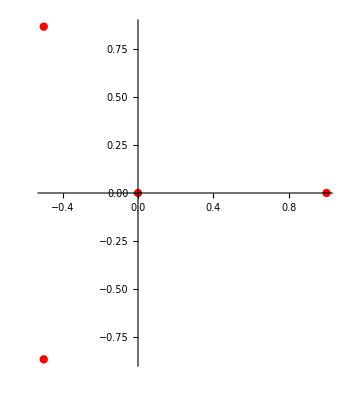

```mathematica
soluiru[z^2-Conjugate[z],z]
```

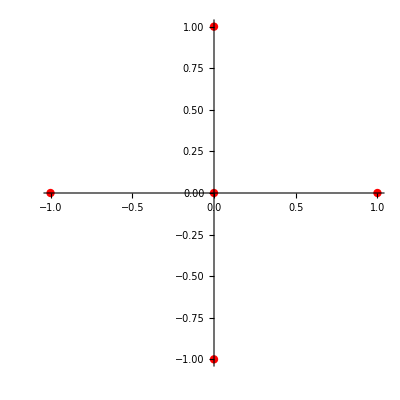

```mathematica
soluiru[z^3-Conjugate[z],z]
```

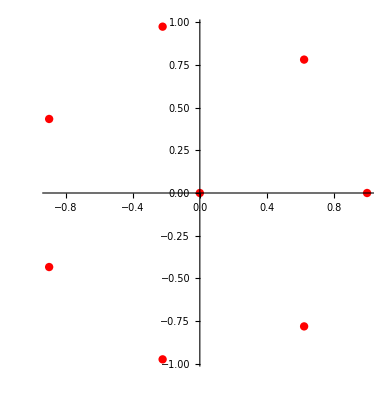

```mathematica
soluiru[z^6-Conjugate[z],z]
```

# Konjugatuaren ekuazioak

Horrela esango diegu 𝓏^𝓃==𝓏̄ motako ekuazioei. Ekuazio horien soluzio kopurua ez da mailak adierazten duena. Hori nola gertatzen den ulertzeko asmoz, atal honetan, eskuz egingo genukeen ebazpena egingo dugu.

## Ekuazioaren soluzioak

Ekuazioa ebazteko koordenatu polarrak erabiliko ditugu; beraz, 𝓏==ρ_θ eta 𝓏̄==ρ_-θ idatziko ditugu. Berreketaren definizioa erabiliz, (ρ_θ)^𝓃==(ρ^𝓃)_𝓃θ da; beraz, bi ekuazio aterako ditugu: moduluen ekuazioa, ρ^𝓃==ρ, ρ≥0 izanik, eta argumentuen ekuazioa, 𝓃θ==-θ+2𝓀π, 𝓀∈ℤ izanik. Ekuazio horiek ebatzi behar ditugu eta soluzioekin konjugatuaren ekuazioaren soluzioak lortu; ondoren irudikatuko ditugu.

Moduluen ekuazioak bi emaitza ditu: ρ==0 eta ρ==1.

23) Zer esanahi geometriko du lehenengo emaitzak (ρ==0)?

Modulua 0 da beraz emaitza planoko puntu bat izango da. Zein?

24) Zer esanahi geometriko du bigarren emaitzak (ρ==1)?

Kasu honetan modulua 1 denez, bigarren emaitzak 1 erradioko zirkunferentzia batean egongo dira

Koordenatu polerratarako aldagai-aldaketaren formulak, 𝓍==ρ Cos θ eta 𝓎==ρ Sin θ, erabiliko ditugu soluzioen koordenatuak kalkulatzeko; ρ==1 denez, koordenatuak 𝓍==Cos θ eta 𝓎==Sin θ izango dira.

Orain, argumentuen ekuazioa ebatziko dugu: (𝓃+1)θ==2𝓀π, 𝓀∈ℤ izanik; hortik,  θ==(2𝓀π)/(𝓃+1), 𝓀∈ℤ izanik. Kontuan izan behar dugu 𝓀 bakoitzeko soluzio bat izango dugula;

25) Zenbat soluzio izango ditu aurreko ekuazioak?

Infinitu n soluzio izango ditu k-ren balioaren arabera k edozein zenbaki oso izan daitekeelako eta θ angelua denez  2π-ko diferentzia dituzten angelu guztiak berdinak izango dira

```mathematica
argtuak[n_,k_] := Flatten[  Table[ Solve[n t == -t + 2 l Pi], {l,-k,k}]]
```

26) Zenbat emaitza ematen ditu aurreko funtzioak? Zerbait antzeman duzu emaitzetan?

Erantzuna?

```mathematica
argtuak[1,3]
```

{t→-3 π,t→-2 π,t→-π,t→0,t→π,t→2 π,t→3 π}

Soluzioak zenbaki erreal gisa zuzen batean daude; zuzen horretan infinitu soluzio daude. Baina, soluzioak angelu gisa interpretatzen baditugu, lehenengo bira eman eta gero errpikatu egingo dira. Ez badugu errepikatzea nahi, nahikoa izango dugu 𝓀 == 0,1,...,𝓃 balioak hartzea. Horrek esan nahi du 𝓃+1 soluzio izango ditugula. Orduan, aurreko funtzioa zorroztu ahal izango dugu emaitza horiek bakarrik lortzeko. Horrez gain, irteera puntuan zerrenda gisa nahi dugu, ez erregelen zerrenda gisa; hori ere kontuan hartuko dugu funtzio berrian:

```mathematica
solarg[n_] :=t /. Table[ Flatten[  Solve[n t == -t + 2 k Pi]], {k,0,n}]
solarg[3]
```

{0,π/2,π,(3 π)/2}

Soluzioen argumentuak ezagututa, ρ==1 ematzari dagozkion soluzioen koordenatuak kalkulatuko ditugu:

```mathematica
solpun[n_] := Table[ {Cos[solarg[n][[i]]],Sin[solarg[n][[i]]]}, {i,n+1} ]
solpun[4]
```

{{1,0},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{1/4 (-1-√5),-√(5/8-(√5)/8)},{1/4 (-1+√5),-√(5/8+(√5)/8)}}

27) Zer adierazpide erabiltzen da aurreko funtzioan? Zer adierazpide dute emaitzek?

Adierazpide trigonometrikoa erabiltzen da aurreko funtzioan, emaitzek ordea adierazpen binomiala  dute. Geometrikoa
Binomiala edo geometrikoa?

Aurreko puntuei ρ==0 emaitzari dagokion puntua, jatorria, erantsiko diegu:

```mathematica
solguz[n_] := Append[ solpun[n], {0,0} ]
solguz[4]
```

{{1,0},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{1/4 (-1-√5),-√(5/8-(√5)/8)},{1/4 (-1+√5),-√(5/8+(√5)/8)},{0,0}}

## Soluzioen irudiak

Orain, puntuak OXY planoan irudikatuko ditugu:

```mathematica
koniru[n_] := ListPlot[ solguz[n], PlotStyle->{RGBColor[1,0,0],PointSize[0.015]},AspectRatio->Automatic ]
koniru[6]
```

-Graphics-

Bukatzeko, ekuazioaren soluzioez gain, 1 erradioko zirkunferentzia ere irudikatuko dugu:

```mathematica
koniruoso[n_] :=Show[ Graphics[Circle[{0,0}],Axes->True,PlotRange->All],koniru[n]]
```

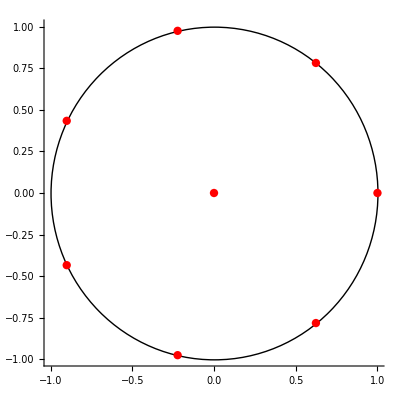

```mathematica
koniruoso[6]
```

28) Ebatz itzazu ariketen orriko ariketa batzuk aurreko funtzioekin. Esan ezazu zer ariketak diren.

20.2 ariketa.

z^5=𝓏̄

```mathematica
solarg[5]
```

{0,π/3,(2 π)/3,π,(4 π)/3,(5 π)/3}

```mathematica
solpun[5]
```

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2}}

```mathematica
solguz[5]
```

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{0,0}}

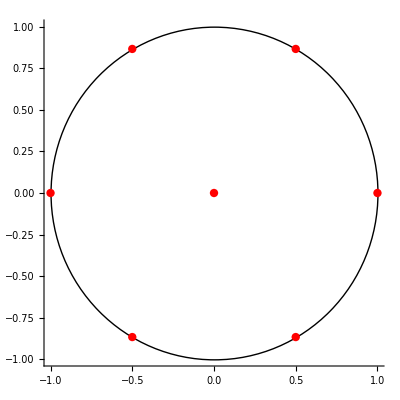

```mathematica
koniruoso[5]
```

20.14 ariketa.

z^2=𝓏̄

```mathematica
solarg[2]
```

{0,(2 π)/3,(4 π)/3}

```mathematica
solpun[2]
```

{{1,0},{-1/2,(√3)/2},{-1/2,-(√3)/2}}

```mathematica
solguz[2]
```

{{1,0},{-1/2,(√3)/2},{-1/2,-(√3)/2},{0,0}}

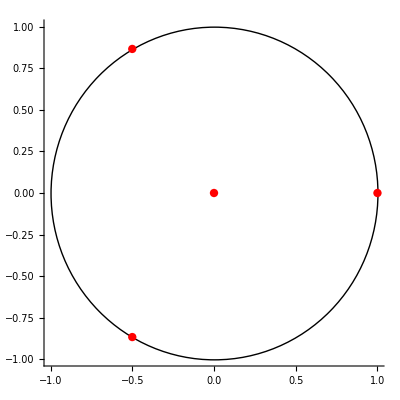

```mathematica
koniruoso[2]
```